```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
wf1AllImPP=Get[NotebookDirectory[]<>"wf1AllIm.txt"][[1]];
wf1AllRePP=Get[NotebookDirectory[]<>"wf1AllRe.txt"][[1]];
wf2AllImPP=Get[NotebookDirectory[]<>"wf2AllIm.txt"][[1]];
wf2AllRePP=Get[NotebookDirectory[]<>"wf2AllRe.txt"][[1]];
wf1AllImMM=Get[NotebookDirectory[]<>"wf1AllImmm.txt"][[1]];
wf1AllReMM=Get[NotebookDirectory[]<>"wf1AllRemm.txt"][[1]];
wf2AllImMM=Get[NotebookDirectory[]<>"wf2AllImmm.txt"][[1]];
wf2AllReMM=Get[NotebookDirectory[]<>"wf2AllRemm.txt"][[1]];
```

/Users/gangchen/Documents/GitHub/WaveFormOneLoopQM

```mathematica
wf1PP=((Part[#,2]&/@ wf1AllRePP)+I (Part[#,2]&/@ wf1AllImPP));
wf2PP=((Part[#,2]&/@ wf2AllRePP)+I (Part[#,2]&/@ wf2AllImPP));
wf1MM=((Part[#,2]&/@ wf1AllReMM)+I (Part[#,2]&/@ wf1AllImMM));
wf2MM=((Part[#,2]&/@ wf2AllReMM)+I (Part[#,2]&/@ wf2AllImMM));
```

```mathematica
ClearAll[wfPP,wfMM]
wfPP[μ_]:=(1-μ)wf1PP+μ wf2PP;
wfMM[μ_]:=(1-μ)wf1MM+μ wf2MM;
```

```mathematica
omegas=Transpose[wf1AllImPP][[1]]
```

{0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.,5.1,5.2,5.3,5.4,5.5,5.6,5.7,5.8,5.9,6.,6.1,6.2,6.3,6.4,6.5,6.6,6.7,6.8,6.9,7.,7.1,7.2,7.3,7.4,7.5,7.6,7.7,7.8,7.9,8.,8.1,8.2,8.3,8.4,8.5,8.6,8.7,8.8,8.9,9.,9.1,9.2,9.3,9.4,9.5,9.6,9.7,9.8,9.9,10.,10.1,10.2,10.3,10.4,10.5,10.6,10.7,10.8,10.9,11.,11.1,11.2,11.3,11.4,11.5,11.6,11.7,11.8,11.9,12.,12.1,12.2,12.3,12.4,12.5,12.6,12.7,12.8,12.9,13.,13.1,13.2,13.3,13.4,13.5,13.6,13.7,13.8,13.9,14.,14.1,14.2,14.3,14.4,14.5,14.6,14.7,14.8,14.9,15.,15.1,15.2,15.3,15.4,15.5,15.6,15.7,15.8,15.9,16.,16.1,16.2,16.3,16.4,16.5,16.6,16.7,16.8,16.9,17.,17.1,17.2,17.3,17.4,17.5,17.6,17.7,17.8,17.9,18.,18.1,18.2,18.3,18.4,18.5,18.6,18.7,18.8,18.9,19.,19.1,19.2,19.3,19.4,19.5,19.6,19.7,19.8,19.9,20.}

```mathematica
(*ComplexListPlot[Table[wfPP[μ],{μ,0.1,0.9,0.2}]]
ComplexListPlot[Table[wfMM[μ],{μ,0.1,0.9,0.2}]]*)
```

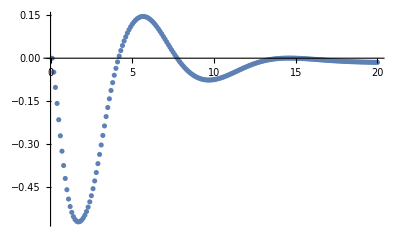

wfMM

```mathematica
wf1AllImPP;
ListPlot[%,PlotRange->All]
```

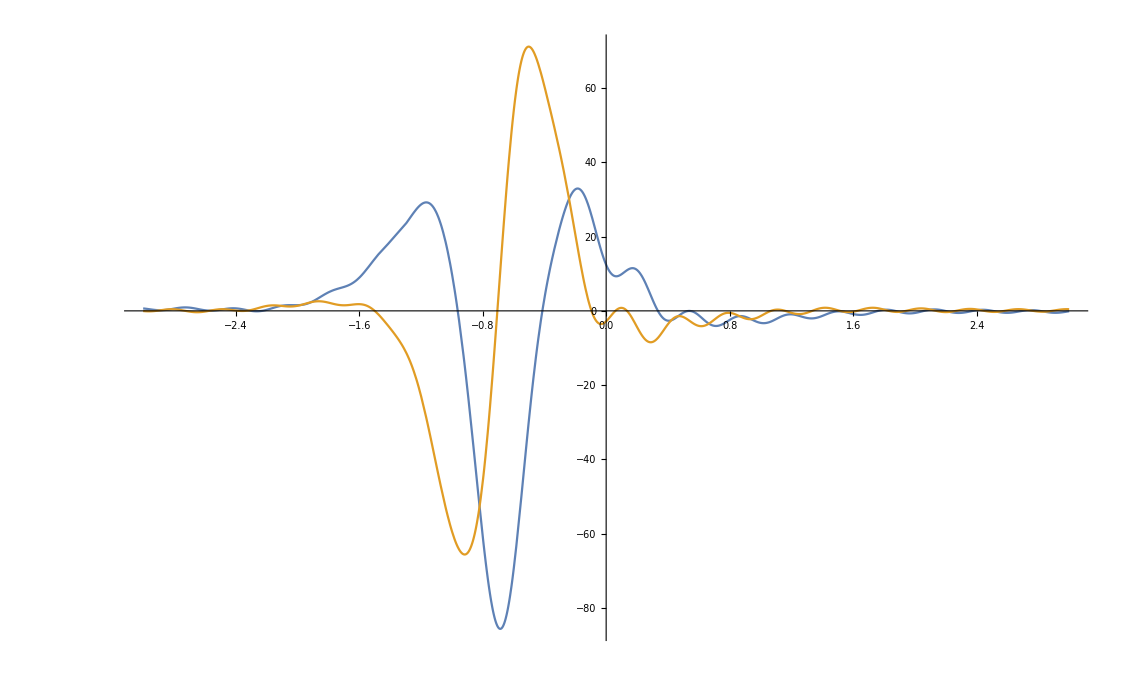

```mathematica
exp1=Table[Exp[-I ω t]/.ω->i,{i,omegas}];
exp2=Table[Exp[I ω t]/.ω->i,{i,omegas}];
wft=Table[Total[ 0.1*(exp1*wfMM[μ]+exp2*Conjugate[wfPP[μ]])],{μ,0.5,0.5,0.4}];
Plot[{Re/@wft,Im/@wft},{t,-3,3},PlotRange->All]
```

{{-3.,0.653654},{-2.95,0.388072},{-2.9,0.183194},{-2.85,0.2691},{-2.8,0.602441},{-2.75,0.89545},{-2.7,0.875221},{-2.65,0.538932},{-2.6,0.166379},{-2.55,0.0698123},{-2.5,0.306087},{-2.45,0.619327},{-2.4,0.67618},{-2.35,0.38398},{-2.3,-0.00347704},{-2.25,-0.10022},{-2.2,0.265528},{-2.15,0.892016},{-2.1,1.38814},{-2.05,1.5417},{-2.,1.53292},{-1.95,1.78579},{-1.9,2.5817},{-1.85,3.79016},{-1.8,4.97886},{-1.75,5.8206},{-1.7,6.43013},{-1.65,7.30869},{-1.6,8.9242},{-1.55,11.2974},{-1.5,13.9777},{-1.45,16.4469},{-1.4,18.5845},{-1.35,20.7493},{-1.3,23.3544},{-1.25,26.2805},{-1.2,28.6362},{-1.15,29.0863},{-1.1,26.4728},{-1.05,20.2096},{-1.,10.1884},{-0.95,-3.54406},{-0.9,-20.7883},{-0.85,-40.6214},{-0.8,-60.6575},{-0.75,-76.9753},{-0.7,-85.2539},{-0.65,-82.7439},{-0.6,-69.8762},{-0.55,-50.3147},{-0.5,-29.2252},{-0.45,-10.7959},{-0.4,3.37559},{-0.35,14.0363},{-0.3,22.5551},{-0.25,29.191},{-0.2,32.7412},{-0.15,31.7854},{-0.1,26.4035},{-0.05,18.8374},{0.,12.4138},{0.05,9.47203},{0.1,9.88075},{0.15,11.303},{0.2,11.0151},{0.25,7.89379},{0.3,3.09395},{0.35,-1.00155},{0.4,-2.64472},{0.45,-1.92871},{0.5,-0.486623},{0.55,-0.066077},{0.6,-1.19758},{0.65,-2.98115},{0.7,-4.02857},{0.75,-3.67473},{0.8,-2.44883},{0.85,-1.50402},{0.9,-1.58961},{0.95,-2.46991},{1.,-3.23208},{1.05,-3.13679},{1.1,-2.23839},{1.15,-1.26686},{1.2,-0.938398},{1.25,-1.33805},{1.3,-1.90256},{1.35,-1.97034},{1.4,-1.37447},{1.45,-0.556234},{1.5,-0.13338},{1.55,-0.340999},{1.6,-0.847424},{1.65,-1.08478},{1.7,-0.769879},{1.75,-0.141441},{1.8,0.28164},{1.85,0.179885},{1.9,-0.289515},{1.95,-0.65513},{2.,-0.566967},{2.05,-0.103213},{2.1,0.319949},{2.15,0.336526},{2.2,-0.043674},{2.25,-0.460271},{2.3,-0.540024},{2.35,-0.23079},{2.4,0.167176},{2.45,0.287251},{2.5,0.0292676},{2.55,-0.361873},{2.6,-0.53175},{2.65,-0.340978},{2.7,0.0174926},{2.75,0.206098},{2.8,0.0541678},{2.85,-0.293069},{2.9,-0.51701},{2.95,-0.42056},{3.,-0.103088}}

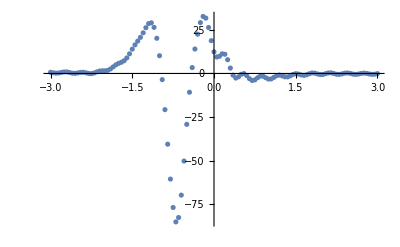

```mathematica
Table[{ii,wft[[1]]/.t->ii//Re},{ii,-3,3,0.05}]
ListPlot[%,PlotRange->All]
```

{{-3.,-0.0433652},{-2.95,-0.118112},{-2.9,0.0866405},{-2.85,0.363522},{-2.8,0.426374},{-2.75,0.17733},{-2.7,-0.191999},{-2.65,-0.365645},{-2.6,-0.189765},{-2.55,0.182779},{-2.5,0.429436},{-2.45,0.357838},{-2.4,0.0932737},{-2.35,-0.0260886},{-2.3,0.241042},{-2.25,0.806957},{-2.2,1.3211},{-2.15,1.484},{-2.1,1.32415},{-2.05,1.17627},{-2.,1.36939},{-1.95,1.90657},{-1.9,2.43851},{-1.85,2.57002},{-1.8,2.22544},{-1.75,1.72882},{-1.7,1.50434},{-1.65,1.65477},{-1.6,1.80459},{-1.55,1.36712},{-1.5,0.00557479},{-1.45,-2.13657},{-1.4,-4.66743},{-1.35,-7.44958},{-1.3,-10.912},{-1.25,-15.8512},{-1.2,-22.8441},{-1.15,-31.7408},{-1.1,-41.6296},{-1.05,-51.2298},{-1.,-59.2741},{-0.95,-64.4969},{-0.9,-65.3171},{-0.85,-59.7706},{-0.8,-46.1884},{-0.75,-24.4869},{-0.7,2.79062},{-0.65,30.6732},{-0.6,53.4795},{-0.55,67.2177},{-0.5,71.1939},{-0.45,67.7779},{-0.4,60.521},{-0.35,51.9822},{-0.3,42.772},{-0.25,32.3375},{-0.2,20.6399},{-0.15,9.205},{-0.1,0.596017},{-0.05,-3.30777},{0.,-2.8138},{0.05,-0.417145},{0.1,0.805559},{0.15,-0.76538},{0.2,-4.3468},{0.25,-7.57146},{0.3,-8.38296},{0.35,-6.53425},{0.4,-3.60482},{0.45,-1.65466},{0.5,-1.66447},{0.55,-2.97429},{0.6,-4.04357},{0.65,-3.79141},{0.7,-2.39443},{0.75,-0.970748},{0.8,-0.535157},{0.85,-1.16237},{0.9,-2.02691},{0.95,-2.19459},{1.,-1.42553},{1.05,-0.309649},{1.1,0.317365},{1.15,0.113464},{1.2,-0.522397},{1.25,-0.865093},{1.3,-0.525625},{1.35,0.234892},{1.4,0.78637},{1.45,0.714965},{1.5,0.175874},{1.55,-0.281567},{1.6,-0.227113},{1.65,0.275056},{1.7,0.753942},{1.75,0.77751},{1.8,0.339473},{1.85,-0.154936},{1.9,-0.271004},{1.95,0.0651791},{2.,0.517501},{2.05,0.659806},{2.1,0.362092},{2.15,-0.105391},{2.2,-0.330707},{2.25,-0.134302},{2.3,0.280979},{2.35,0.52826},{2.4,0.39064},{2.45,0.00716036},{2.5,-0.268462},{2.55,-0.195313},{2.6,0.143138},{2.65,0.428635},{2.7,0.405624},{2.75,0.109848},{2.8,-0.175626},{2.85,-0.18674},{2.9,0.0821944},{2.95,0.381973},{3.,0.443293}}

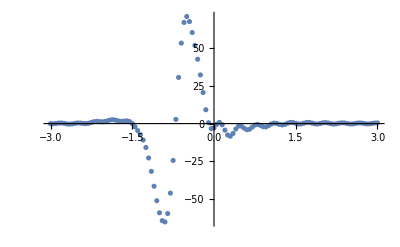

```mathematica
Table[{ii,wft[[1]]/.t->ii//Im},{ii,-3,3,0.05}]
ListPlot[%,PlotRange->All]
```

```mathematica
(*f[x_]:=Exp[-x]
Plot[HeavisideTheta[x]f[x],{x,-10,10},PlotRange->All]
FourierTransform[HeavisideTheta[x]f[x],x,t]
Plot[{Re[%],Im[%]},{t,-10,10}]*)
```

```mathematica
(*$interval=0.1;
$finiteSize=2;
num=Table[N[f[x],10],{x,0,$finiteSize,$interval}]
ListPlot[Transpose[{Table[x,{x,0,$finiteSize,$interval}],%}]]
expNum=Table[Exp[I x t],{x,0,$finiteSize,$interval}]
0.1*num.expNum;
Plot[{Re[%],Im[%]},{t,-10,10}]*)
```